## Problems: Torque Control With a Swarm of Norm,Triangularly,Uniform distributed Particles Under Global Control Given a swarm of particles, whose positions are normally distributed, and a pivoted object, where should the swarm hit to generate the maximum torque? related problem: shooting a railroad track switch with a shotgun. F = force provided by entire swarm N = number of particles F/N = force per particle ⅇ^(-(x-μ)^2/(2 σ^2))

### Problem 1: marginalizing to 1 dimension, not thinking about distributed time of impact this is only a one-pass of the swarm at the object. The kilobots are pushing continuously. (math is for one step, real world is an iterative process)

```mathematica
pdfUniform[x_,μ_,σ_]:=Piecewise[{{1/(2 √3 σ), μ-√3 σ≤x≤μ+√3 σ}, {0, True}}]
```

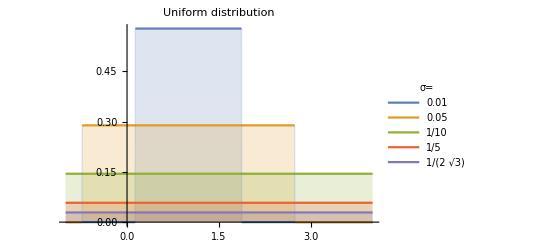

```mathematica
sigs = {0.1,0.5,1,2,5/√3,5}/10;
Plot[Evaluate[Table[pdfUniform[x,1,σ],{σ,{1/2,1,2,5,10}}]],{x,-1,4},Filling->Axis,PlotRange->All,AxesOrigin->{0,0},PlotLegends->Placed[LineLegend[sigs,LabelStyle->{Black,Bold,8},LegendLabel->"σ="],{0.85,0.55}],PlotLabel->"Uniform distribution"]
Export["../abecker/SwarmPublications/JournalTorqueControl/pictures/pdf/Uniform.pdf",%];
```

```mathematica
pdfTriangle[x_,μ_,σ_]:=Piecewise[{{(x-μ+√6 σ)/(6 σ^2), μ-√6 σ≤x≤μ}, {(-x+μ+√6 σ)/(6 σ^2), μ<x≤μ+√6 σ}, {0, True}}]
```

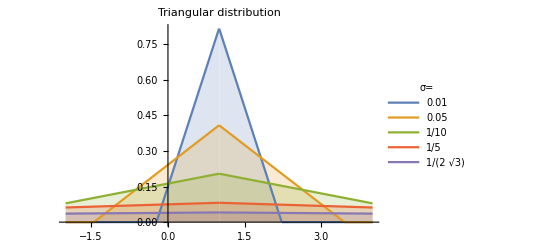

```mathematica
Plot[Evaluate[Table[pdfTriangle[x,1,σ],{σ,{1/2,1,2,5,10}}]],{x,-2,4},Filling->Axis,PlotRange->All,AxesOrigin->{0,0},PlotLegends->Placed[LineLegend[sigs,LabelStyle->{Black,Bold,8},LegendLabel->"σ="],{0.75,0.55}],PlotLabel->"Triangular distribution"]
Export["../abecker/SwarmPublications/JournalTorqueControl/pictures/pdf/Triangular.pdf",%];
```

```mathematica
pdfNormal[x_,μ_,σ_]:=1/(√(2 π) σ) ⅇ^(-(x-μ)^2/(2 σ^2))
```

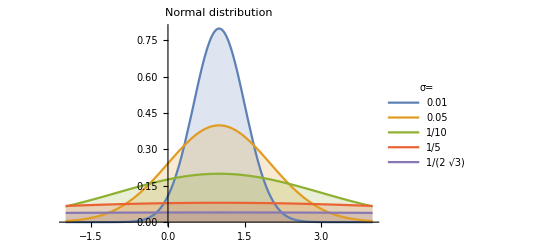

```mathematica
Plot[Evaluate[pdfNormal[x,1,σ]/.σ->{1/2,1,2,5,10}],{x,-2,4},Filling->Axis,PlotRange->All,PlotLegends->Placed[LineLegend[sigs,LabelStyle->{Black,Bold,8},LegendLabel->"σ="],{0.85,0.55}],PlotLabel->"Normal distribution"]
Export["../abecker/SwarmPublications/JournalTorqueControl/pictures/pdf/Normal.pdf",%];
```

```mathematica
TorquePivotUni[μ_,σ_]:=Module[{lowlim =Max[0,μ-√3 σ],uplim =  Min[1,μ+√3 σ]},
If[uplim>lowlim,-lowlim^2/(4 √3 σ)+uplim^2/(4 √3 σ),0]];
```

```mathematica
TorquePivotTriATB[μ_,σ_]:=Module[{lowlim1 =Max[0,μ-√6 σ],uplim1 =  Min[1,μ],lowlim2 =Max[0,μ],uplim2 =  Min[1,μ+√6 σ]},
If[uplim1>lowlim1,(-2 lowlim1^3+3 lowlim1^2 (μ-√6 σ)+uplim1^2 (2 uplim1-3 μ+3 √6 σ))/(36 σ^2),0]+
If[uplim2>lowlim2,(2 lowlim2^3-3 lowlim2^2 (μ+√6 σ)+uplim2^2 (-2 uplim2+3 (μ+√6 σ)))/(36 σ^2),0]]
```

```mathematica
TorquePivotNorm[μ_,σ_]:=((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-μ^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])
```

```mathematica
sigs = {0.1,0.5,1,2,5/√3,5}/10;
(*TODO: place legend inside the plot*)
Plot[Evaluate[Table[TorquePivotUni[μ,σ],{σ,sigs}]],{μ,-1,4},PlotRange->All,PlotLegends->Placed[LineLegend[sigs,LabelStyle->{Black,Bold,8},LegendLabel->"σ="],{0.75,0.55}],AxesLabel->{"μ","Torque"},Epilog->{Line[{{1/2,0},{1/2,1}}]}]
Export["../abecker/SwarmPublications/JournalTorqueControl/pictures/pdf/TorqueUni.pdf",%];
```

```mathematica
sigs = {0.1,0.5,1,2,5/√3,5}/10;
(*TODO: place legend inside the plot*)
Plot[Evaluate[Table[TorquePivotTriATB[μ,σ],{σ,sigs}]],{μ,-2,4},PlotRange->All,PlotLegends->Placed[LineLegend[sigs,LabelStyle->{Black,Bold,8},LegendLabel->"σ="],{0.75,0.55}],AxesLabel->{"μ","Torque"},Epilog->{Line[{{√2/2,0},{√2/2,1}}]}]
Export["../abecker/SwarmPublications/JournalTorqueControl/pictures/pdf/TorqueTri.pdf",%];
```

```mathematica
sigs = {0.1,0.5,1,2,5/√3,5}/10;
(*TODO: place legend inside the plot*)
Plot[Evaluate[TorquePivotNorm[μ,σ]/.{σ->sigs}],{μ,-2,4},PlotRange->All,PlotLegends->Placed[LineLegend[sigs,LabelStyle->{Black,Bold,8},LegendLabel->"σ="],{0.75,0.55}],AxesLabel->{"μ","Torque"}, Epilog->{Line[{{2/3,0},{2/3,1}}]}]
Export["../abecker/SwarmPublications/JournalTorqueControl/pictures/pdf/TorqueNormal.pdf",%];
```

### Comparison Plots

```mathematica
Timing[bestPushNorm=Table[ans=FindMaximum[((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-μ^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)]),{μ,1}];{σ,First@ans,ans⟦2,1,2⟧},{σ,0.01,1,0.01}];]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.12743,Null}

```mathematica
Timing[bestPushUni=Table[ans=FindMaximum[{TorquePivotUni[μ,σ]},{μ,Max[1-σ√3,σ√3]}];{σ,First@ans,ans⟦2,1,2⟧},{σ,0.01,1,0.01}];]
Timing[bestPushUniBot=Table[ans=FindMaximum[{TorquePivotUni[μ,σ]},{μ,1-σ√3}];{σ,First@ans,ans⟦2,1,2⟧},{σ,0.01,1,0.01}];]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

{0.22257,Null}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

General::stop: Further output of FindMaximum :: fmgz will be suppressed during this calculation.

{0.31403,Null}

```mathematica
Last[{0.13768099999999999782929194225289393216`5.15947392496363,Null}]
```

```mathematica
Timing[bestPushTriATB=Table[ans=FindMaximum[{TorquePivotTriATB[μ,σ]},{μ,1}];{σ,First@ans,ans⟦2,1,2⟧},{σ,0.01,1,0.01}];]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

{0.32592,Null}

```mathematica
Timing[bestPushTri=Table[ans=FindMaximum[{TorquePivot[μ,σ]&&μ>0},{μ,1}];{σ,First@ans,ans⟦2,1,2⟧},{σ,0.01,1,0.01}];]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

{6.05867,Null}

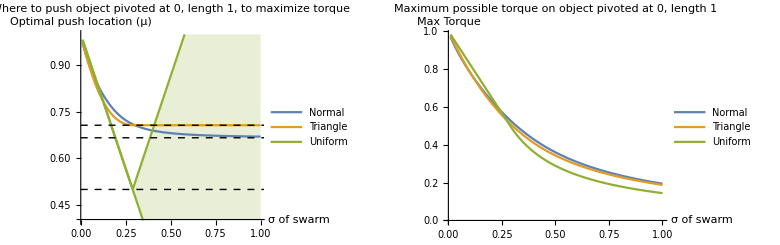

```mathematica
plotBestLocationPivotObject =ListPlot[{
Transpose[{bestPushNorm⟦;;,1⟧,bestPushNorm⟦;;,3⟧}],
Transpose[{bestPushTriATB⟦;;,1⟧,bestPushTriATB⟦;;,3⟧}],
Transpose[{bestPushUni⟦;;,1⟧,bestPushUni⟦;;,3⟧}],
Transpose[{bestPushUniBot⟦;;,1⟧,bestPushUniBot⟦;;,3⟧}]
},AxesLabel->{"σ of swarm","Optimal push location (μ)"},Joined->True,
Filling->{3->{4}},PlotStyle->{Automatic,Automatic,Automatic,ColorData[97,3]},PlotLegends->Placed[LineLegend[{"Normal","Triangle","Uniform"},LabelStyle->{Black,Bold,8}],{0.77,0.75}],Epilog->{Dashed,Line[{{0,2/3},{100,2/3}}],
Line[{{0,√2/2},{100,√2/2}}],
Line[{{0,1/2},{100,1/2}}]
},PlotRange->{Automatic,{0.4,1.0}},
Prolog-> Inset[pivotDrawing[1/10]],ImageSize->Medium,
PlotLabel->"Where to push object pivoted at 0, length 1, to maximize torque"];
Export["../abecker/SwarmPublications/JournalTorqueControl/pictures/pdf/BestLocationPivot.pdf",%];
plotMaxTorquePivotObject=ListPlot[{Transpose[{bestPushNorm⟦;;,1⟧,bestPushNorm⟦;;,2⟧}],Transpose[{bestPushTriATB⟦;;,1⟧,bestPushTriATB⟦;;,2⟧}],
Transpose[{bestPushUni⟦;;,1⟧,bestPushUni⟦;;,2⟧}]}
,AxesLabel->{"σ of swarm","Max Torque"},Joined->True,
PlotLegends->Placed[{"Normal","Triangle","Uniform"},{Right,Top}],ImageSize->Medium,PlotLabel->"Maximum possible torque on object pivoted at 0, length 1",ImageSize->Medium];
Export["../abecker/SwarmPublications/JournalTorqueControl/pictures/pdf/MaxTorquePivot.pdf",%];
GraphicsRow[{plotBestLocationPivotObject,plotMaxTorquePivotObject}]
```

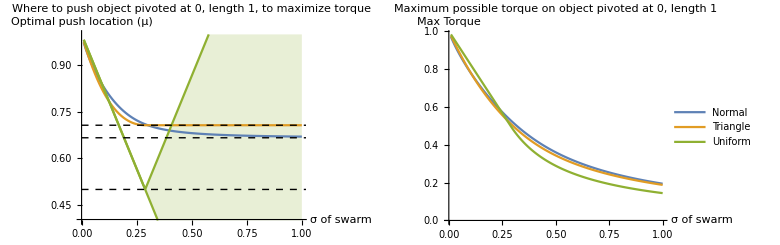

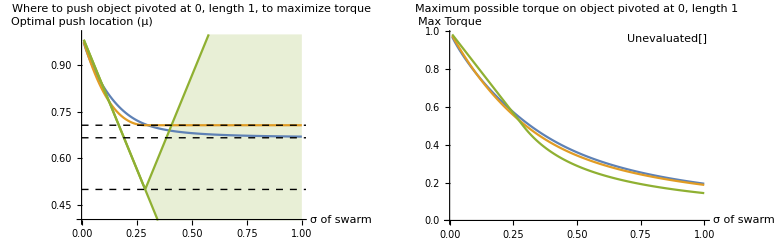

Note :  the optimal μ for uniform distribution is any value between 1 - σ √3 and σ √3

```mathematica
pivotDrawing[σ_]:=Graphics[{
Brown,
Rectangle[{0,-1/10},{1,1/10}],
Blue,Point[{0,0}],
Red,Polygon[{{.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{.75,-3}}],
Black,PointSize[Tiny],Point[RandomVariate[MultinormalDistribution[{1,-5},{{σ,0},{0,σ}}],10^3]]},
PlotRange->{{-1,3},{-8,2}},AxesOrigin->{0,0}]
```

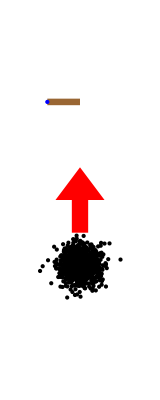
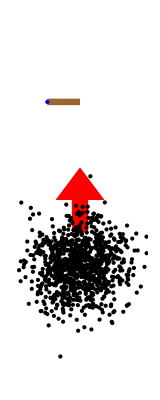
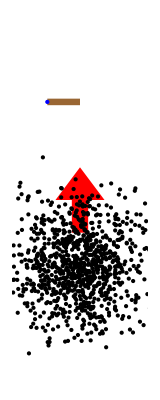
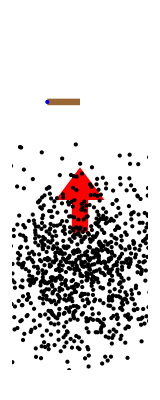

```mathematica
Table[Graphics[{
Brown,
Rectangle[{0,-1/10},{1,1/10}],
Blue,Point[{0,0}],
Red,Polygon[{{.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{.75,-3}}],
Black,PointSize[Tiny],Point[RandomVariate[MultinormalDistribution[{1,-5},{{σ,0},{0,σ}}],10^3]]},
PlotRange->{{-1,3},{-8,2}},AxesOrigin->{0,0}],{σ,{1/10,1/2,1,2}}]
```

### Problem 2: a free object (no pivot point). Where should swarm fit to generate the most torque?

```mathematica
TorqueFreeNorm[μ_,σ_] :=((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-(1+μ)^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[(1+μ)/(√2 σ)])
```

```mathematica
FullSimplify[∫_-1^1 x pdfTriangle[x,μ,σ] ⅆx](*assume the object COM is at 0, and the object extends from -1 to 1*)
```

Piecewise[{{μ, √6 (1+μ)≥6 σ&&√6 μ+6 σ<√6&&σ>0}, {-1/(9 σ^2), (μ==-1&&3 σ≥√6)||(μ<-1&&√6 μ+6 σ>√6)}, {1/(9 σ^2), (μ>1&&√6 (1+μ)≤6 σ)||(μ==1&&3 σ≥√6)}, {-(μ (-3+μ^2))/(18 σ^2), -1<μ<1&&√6 (1+μ)<6 σ&&√6 μ+6 σ≥√6}, {1/2-σ/(√6), μ==1&&0<σ<√(2/3)}, {-1/2+σ/(√6), μ==-1&&0<σ<√(2/3)}, {-(2+μ^3+3 √6 μ^2 σ+3 √6 σ (-1+2 σ^2)-3 μ (1+6 σ^2))/(36 σ^2), √6 μ+6 σ≥√6&&μ<1&&√6 (1+μ)≥6 σ}, {(2+μ^3-3 √6 μ^2 σ+3 √6 σ (1-2 σ^2)+3 μ (-1+6 σ^2))/(36 σ^2), μ>1&&-√6<√6 μ-6 σ<√6}, {(2-μ^3+3 √6 μ^2 σ+3 √6 σ (-1+2 σ^2)+3 μ (1+6 σ^2))/(36 σ^2), μ>-1&&√6 (1+μ)<6 σ&&√6 μ+6 σ<√6}, {(-2+μ^3+3 √6 μ^2 σ+3 √6 σ (-1+2 σ^2)+3 μ (-1+6 σ^2))/(36 σ^2), μ<-1&&-√6<√6 μ+6 σ≤√6}, {0, True}}]

```mathematica
TorqueFreeTri[μ_,σ_]:=Piecewise[{{μ, √6 (1+μ)≥6 σ&&√6 μ+6 σ<√6&&σ>0}, {-1/(9 σ^2), (μ==-1&&3 σ≥√6)||(μ<-1&&√6 μ+6 σ>√6)}, {1/(9 σ^2), (μ>1&&√6 (1+μ)≤6 σ)||(μ==1&&3 σ≥√6)}, {-(μ (-3+μ^2))/(18 σ^2), -1<μ<1&&√6 (1+μ)<6 σ&&√6 μ+6 σ≥√6}, {1/2-σ/(√6), μ==1&&0<σ<√(2/3)}, {-1/2+σ/(√6), μ==-1&&0<σ<√(2/3)}, {-(2+μ^3+3 √6 μ^2 σ+3 √6 σ (-1+2 σ^2)-3 μ (1+6 σ^2))/(36 σ^2), √6 μ+6 σ≥√6&&μ<1&&√6 (1+μ)≥6 σ}, {(2+μ^3-3 √6 μ^2 σ+3 √6 σ (1-2 σ^2)+3 μ (-1+6 σ^2))/(36 σ^2), μ>1&&-√6<√6 μ-6 σ<√6}, {(2-μ^3+3 √6 μ^2 σ+3 √6 σ (-1+2 σ^2)+3 μ (1+6 σ^2))/(36 σ^2), μ>-1&&√6 (1+μ)<6 σ&&√6 μ+6 σ<√6}, {(-2+μ^3+3 √6 μ^2 σ+3 √6 σ (-1+2 σ^2)+3 μ (-1+6 σ^2))/(36 σ^2), μ<-1&&-√6<√6 μ+6 σ≤√6}, {0, True}}]
```

```mathematica
TorquePivotTriFree[μ_,σ_]:=Module[{lowlim1 =Max[-1,μ-√6 σ],uplim1 =  Min[1,μ],lowlim2 =Max[-1,μ],uplim2 =  Min[1,μ+√6 σ]},
If[uplim1>lowlim1,(-2 lowlim1^3+3 lowlim1^2 (μ-√6 σ)+uplim1^2 (2 uplim1-3 μ+3 √6 σ))/(36 σ^2),0]+
If[uplim2>lowlim2,(2 lowlim2^3-3 lowlim2^2 (μ+√6 σ)+uplim2^2 (-2 uplim2+3 (μ+√6 σ)))/(36 σ^2),0]]
(*Module[{lowlim1 =Max[0,μ-√6 σ];uplim1 =  Min[1,μ];lowlim2 =Max[0,μ];uplim2 =  Min[1,μ+√6 σ]},
If[uplim1>lowlim1,∫_lowlim1^uplim1 x (x-μ+√6 σ)/(6 σ^2)ⅆx,0]+
If[uplim2>lowlim2,∫_lowlim2^uplim2 x (-x+μ+√6 σ)/(6 σ^2)ⅆx,0]]*)
```

```mathematica
∫_lowlim^uplim x 1/(2 √3 σ)ⅆx
```

-lowlim^2/(4 √3 σ)+uplim^2/(4 √3 σ)

```mathematica
TorquePivotFreeUni[1/2,2]
```

TorquePivotFreeUni[1/2,2]

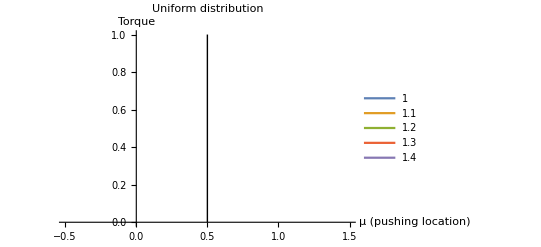

```mathematica
sigs = {1,1.1,1.2,1.3,1.4};
(*TODO: place legend inside the plot*)
Plot[Evaluate[Table[TorquePivotFreeUni[μ,σ],{σ,sigs}]],{μ,-4,4},PlotRange->All,PlotLegends->sigs,AxesLabel->{"μ (pushing location)","Torque"},PlotLabel->"Uniform distribution",Epilog->{Line[{{1/2,0},{1/2,1}}]}]
```

```mathematica
sigs = {0.1,0.5,1,2,5/√3,5,10}/10;
(*TODO: place legend inside the plot*)
Plot[Evaluate[Table[TorquePivotFreeUni[μ,σ],{σ,sigs}]],{μ,-2,2},PlotRange->All,PlotLegends->Placed[LineLegend[sigs,LabelStyle->{Black,Bold,8},LegendLabel->"σ="],{1,0.55}],AxesLabel->{"μ","Torque"},PlotLabel->"Uniform distribution",Epilog->{Line[{{1/2,0},{1/2,1}}]}]
Export["../abecker/SwarmPublications/JournalTorqueControl/pictures/pdf/TorqueUniFree.pdf",%];
```

-Graphics-

```mathematica
TorquePivotFreeUni[μ_,σ_]:=Module[{lowlim =Max[-1,μ-√3 σ],uplim =  Min[1,μ+√3 σ]},
If[uplim>lowlim,-lowlim^2/(4 √3 σ)+uplim^2/(4 √3 σ),0]]
```

```mathematica
Timing[bestPushFreeNorm=Table[ans=FindMaximum[((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-(1+μ)^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[(1+μ)/(√2 σ)]),{μ,1}];{σ,First@ans,ans⟦2,1,2⟧},{σ,0.01,2,0.01}];]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

{0.40952,Null}

```mathematica
Timing[bestPushFreeTri=Table[ans=FindMaximum[TorquePivotTriFree[μ,σ],{μ,Max[1,√6/2σ]}];{σ,First@ans,ans⟦2,1,2⟧},{σ,0.01,2,0.01}];]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

General::stop: Further output of FindMaximum :: fmgz will be suppressed during this calculation.

{0.50404,Null}

```mathematica
Timing[bestPushFreeTriBottom=Table[ans=FindMaximum[TorquePivotTriFree[μ,σ],{μ,1}];{σ,First@ans,ans⟦2,1,2⟧},{σ,0.01,2,0.01}];]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

General::stop: Further output of FindMaximum :: fmgz will be suppressed during this calculation.

{0.48776,Null}

```mathematica
Timing[bestPushFreeUni=Table[ans=FindMaximum[TorquePivotFreeUni[μ,σ],{μ,1+√3/2σ}];{σ,First@ans,ans⟦2,1,2⟧},{σ,0.01,2,0.01}];]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

FindMaximum::fmdig: Working precision MachinePrecision is insufficient to achieve the requested accuracy or precision.

{0.32376,Null}

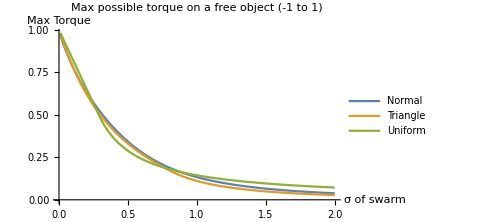

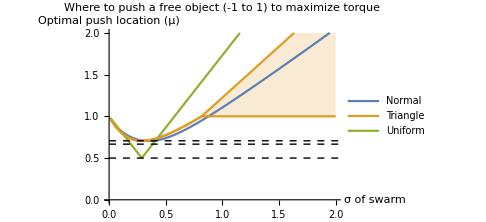

```mathematica
ListPlot[{
Transpose[{bestPushFreeNorm⟦;;,1⟧,bestPushFreeNorm⟦;;,2⟧}],
Transpose[{bestPushFreeTri⟦;;,1⟧,bestPushFreeTri⟦;;,2⟧}],
Transpose[{bestPushFreeUni⟦;;,1⟧,bestPushFreeUni⟦;;,2⟧}]
},AxesLabel->{"σ of swarm","Max Torque"},Joined->True,
PlotLabel->"Max possible torque on  a free object (-1 to 1)",
PlotLegends->Placed[{"Normal","Triangle","Uniform"},{Right,Top}],ImageSize->Medium]
Export["../abecker/SwarmPublications/JournalTorqueControl/pictures/pdf/TorqueFreeComparison.pdf",%];
ListPlot[{
Transpose[{bestPushFreeNorm⟦;;,1⟧,bestPushFreeNorm⟦;;,3⟧}],
Transpose[{bestPushFreeTri⟦;;,1⟧,bestPushFreeTri⟦;;,3⟧}],
Transpose[{bestPushFreeUni⟦;;,1⟧,bestPushFreeUni⟦;;,3⟧}],
Transpose[{bestPushFreeTriBottom⟦;;,1⟧,bestPushFreeTriBottom⟦;;,3⟧}]
},AxesLabel->{"σ of swarm","Optimal push location (μ)"},Filling->{2->{4}},PlotStyle->{Automatic,Automatic,Automatic,ColorData[97,2]},PlotLegends->Placed[{"Normal","Triangle","Uniform"},{Left,Top}],PlotRange->{Automatic,{0,2}},Joined->True,Epilog->{Dashed,Line[{{0,2/3},{100,2/3}}],
Line[{{0,√2/2},{100,√2/2}}],
Line[{{0,1/2},{100,1/2}}]
},PlotLabel->"Where to push a free object (-1 to 1) to maximize torque"]
Export["../abecker/SwarmPublications/JournalTorqueControl/pictures/pdf/TorqueFreeBestPush.pdf",%];
```

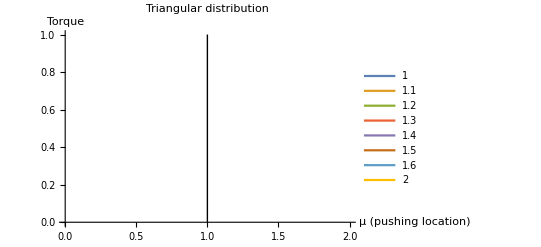

```mathematica
sigs = {1,1.1,1.2,1.3,1.4,1.5,1.6,2};
(*TODO: place legend inside the plot*)
Plot[Evaluate[Table[TorqueFreeNorm[μ,σ],{σ,sigs}]],{μ,-4,4},PlotRange->All,PlotLegends->sigs,AxesLabel->{"μ (pushing location)","Torque"},PlotLabel->"Triangular distribution",Epilog->{Line[{{1,0},{1,1}}]}]
```

```mathematica
sigs = {.3,1,1.1,1.2,1.3,1.4,1.5,1.6,2};
(*TODO: place legend inside the plot*)
Plot[Evaluate[Table[TorquePivotTriFree[μ,σ],{σ,sigs}]],{μ,-4,4},PlotRange->All,PlotLegends->Placed[LineLegend[sigs,LabelStyle->{Black,Bold,8},LegendLabel->"σ="],{1,0.55}],AxesLabel->{"μ","Torque"},PlotLabel->"Triangular distribution",Epilog->{Line[{{1,0},{1,1}}]}]
Export["../abecker/SwarmPublications/JournalTorqueControl/pictures/pdf/TorqueTriFree.pdf",%];
```

-Graphics-

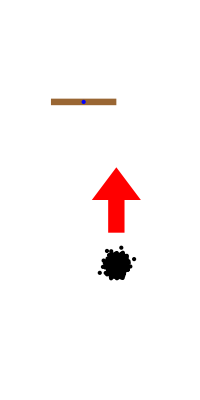
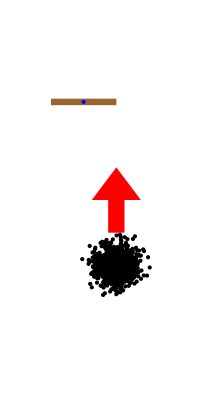
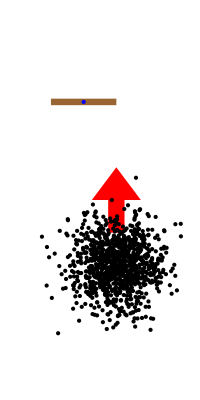
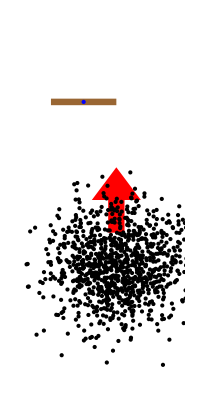
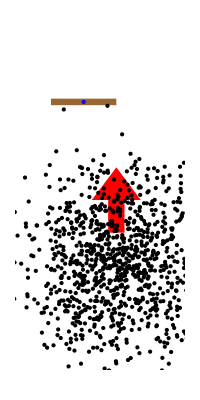

```mathematica
Table[Graphics[{
Brown,
Rectangle[{-1,-1/10},{1,1/10}],
Blue,Point[{0,0}],
Red,Polygon[{{.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{.75,-3}}],
Black,PointSize[Tiny],Point[RandomVariate[MultinormalDistribution[{1,-5},{{σ,0},{0,σ}}],10^3]]
},
PlotRange->{{-2,3},{-8,2}},AxesOrigin->{0,0}],{σ,{1/50,1/10,1/2,1,2}}]
```

```mathematica
{{.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{.75,-3}}
```

{{0.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{0.75,-3}}

### Problem 3: given a variance σ if you push at location μ, with velocity v (everyone not in contact with the object moves at velocity v) , and variance bound σ_max, how long before you need to switch to variance control mode?

```mathematica
Solve[D(-2μ^3 + 3μ+ 3 6^0.5 - 2)==0, {μ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{μ→-0.871067-0.881065 ⅈ},{μ→-0.871067+0.881065 ⅈ},{μ→1.74213}}

```mathematica
{{μ->-((110.58862657687108-191.54511997040254 ⅈ)/(-4.3279414*^7+1.59018721*^8 σ+√(9.36553838091698*^14-1.3764474119818988*^16 σ+2.528695362847584*^16 σ^2))^(1/3))-(0.0011303151496606342+0.0019577632677770375 ⅈ) (-4.3279414*^7+1.59018721*^8 σ+√(9.36553838091698*^14-1.3764474119818988*^16 σ+2.528695362847584*^16 σ^2))^(1/3)},{μ->-((110.58862657687108+191.54511997040254 ⅈ)/(-4.3279414*^7+1.59018721*^8 σ+√(9.36553838091698*^14-1.3764474119818988*^16 σ+2.528695362847584*^16 σ^2))^(1/3))-(0.0011303151496606342-0.0019577632677770375 ⅈ) (-4.3279414*^7+1.59018721*^8 σ+√(9.36553838091698*^14-1.3764474119818988*^16 σ+2.528695362847584*^16 σ^2))^(1/3)},{μ->221.17725315374216/(-4.3279414*^7+1.59018721*^8 σ+√(9.36553838091698*^14-1.3764474119818988*^16 σ+2.528695362847584*^16 σ^2))^(1/3)+0.0022606302993212683 (-4.3279414*^7+1.59018721*^8 σ+√(9.36553838091698*^14-1.3764474119818988*^16 σ+2.528695362847584*^16 σ^2))^(1/

3)}}
```